## 关联勒让德方程的一些分析：

寻找其与勒让德方程的关系，代入 ，可以得到：

{(l+l^2-m (1+m)) u[x]-2 (1+m) x u'[x]-(-1+x^2) u''[x]}=0

{(l+l^2) u[x]-2 x u'[x]-(-1+x^2) u''[x]}=0

{(-2+l+l^2-3 m-m^2) u'[x]-2 (2+m) x u''[x]-(-1+x^2) u^(3)[x]}=0

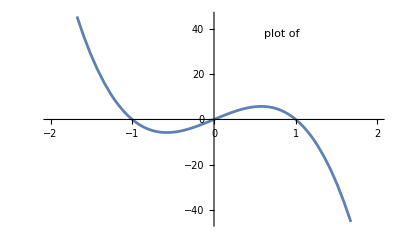

```mathematica
y=(1-x^2)^{m/2} u[x];
y2 = D[y,{x,2}];
y1 = D[y,x];
alp = Simplify[Collect[(1-x^2)*y2-2*x*y1+(l(l+1)-m^2/(1-x^2))*y,\
{u''[x],u'[x],u[x]}]/(1-x^2)^{m/2}];
Print[alp,"=",0];
(*m=0时为勒让德方程*)
Print[alp/. m->0,"=",0];
(*对alp进行求导*)
alpd = Simplify[Collect[D[alp,x],{u'[x],u''[x]}]];
Print[alpd,"=",0];
Plot[LegendreP[3,2,x],{x,-2,2},PlotLegends->Placed["plot of ",{0.7,0.9}]]
```

对比alp=0和alpd=0可以得到关联勒让德方程的解和勒让德方程的解的联系：
解从变为时，m增加了1，因此m从0增加到1，就是求m阶导数：

## 勒让德多项式的生成函数

定义生成函数，并将其展开：

```mathematica
Φ = (1-2*x*h+h^2)^{-1/2} (*h<1*);
Collect[Series[Φ,{x,h/2,2}],{h,h^2,h^3,h^4}]
```

{1+(3 h^4)/8+h x-(3 h^3 x)/2+h^2 (-1/2+(3 x^2)/2)}

我们发现该多项式关于 的系数为，在一些实际应用中我们可以使用
这种方法进行展开。下面给出势能的多级展开为例子：

当时，取相应的勒让德多项式，积分内的式子可以表示为:

```mathematica
Simplify[V=(r^l/R^{l+1})*LegendreP[l,x]];
Table[V/.{l->i,x->Cos[]},{i,0,2}]
```

{{1/R},{(r Cos[θ])/R^2},{(r^2 (-1+3 Cos[θ]^2))/(2 R^3)}}

第一个为点电荷的势能，第二个为电偶极矩的势能，第三个为电四极矩的势能。

## 贝塞尔方程

standard form:

方程的解就是Bessel函数，

```mathematica
DSolve[x^2*y''[x]+x*y'[x]+(x^2-p^2)*y[x]==0,y[x],x]
```

{{y[x]→BesselJ[p,x] C[1]+BesselY[p,x] C[2]}}

其中BesselJ是第一类贝塞尔函数,BesselY是第二类贝塞尔函数，又叫neumann或者weber函数

```mathematica
Series[BesselJ[0,x],{x,0,5}];
Series[BesselY[-2,x],{x,0,5}]
```

-4/(π x^2)-1/π+((-3+4 EulerGamma-4 Log[2]+4 Log[x]) x^2)/(16 π)+((17-12 EulerGamma+12 Log[2]-12 Log[x]) x^4)/(576 π)+O[x]^6

```mathematica
TrueQ[BesselJ[2,x]==(-1)^2 BesselJ[-2,x]]
```

True